# Introducció al Mathematica

## Primera secció

Part 1

Part 2

Shift + Enter / Enter numèric per executar una comanda

```mathematica
3+2
```

5

```mathematica
Log[2]
```

Log[2]

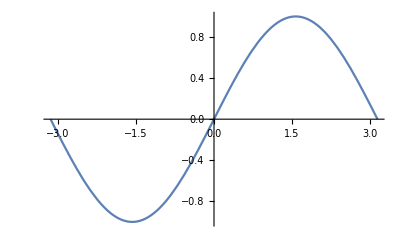

```mathematica
Plot[Sin[x], {x,-Pi,Pi}]
```

```mathematica
%
```

-Graphics-

```mathematica
%1
```

5

Aquests són els objectes amb els que treballarem:

1. Nombres

2. Variables

3. Llistes

4. Definir  funcions

5. Programes interns Mathematica

6. Programes

Nombres / Variables

```mathematica
10
```

```mathematica
Pi
```

```mathematica
3*I + 2
```

```mathematica
nom = "adriana"
```

adriana

```mathematica
cognom = "moya
```

```mathematica
alumnes = 70
```

```mathematica
grups = 3
```

```mathematica
alumnesPerGrup = alumnes/grups
```

70/3

```mathematica
IntegerPart[alumnesPerGrup]
```

23

```mathematica
alumnes = 70
```

70

```mathematica
grups = 3
```

3

```mathematica
alumnesPerGrup = alumnes/grups
```

70/3

Podem borrar el contingut d’una variable:

```mathematica
Clear[alumnes]
```

Llistes:

```mathematica
nombres = {1,2,3,4}
```

{1,2,3,4}

```mathematica
nombres*2
```

{2,4,6,8}

```mathematica
mesNombres = Table[2*n, {n,0, 50}]
```

{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100}

```mathematica
matriu = Table[i+j, {i,1,3},{j,1,4}]
```

{{2,3,4,5},{3,4,5,6},{4,5,6,7}}

```mathematica
MatrixForm[matriu]
```

(2 | 3 | 4 | 5
3 | 4 | 5 | 6
4 | 5 | 6 | 7)

Volem saber quins de vosaltres teniu un niub parell:

```mathematica
?Select
```

```mathematica
niubs=Import["D:niubstf.csv", "List"]
```

```mathematica
Select[niubs, EvenQ]
```

```mathematica
Select[niubs,PrimeQ]
```

```mathematica
Select[niubs, Mod[#, 3]==0&]
```

Definir  funcions

```mathematica
f[x_]:=x^4-1
```

```mathematica
f[3]
```

80

```mathematica
g=Function[x, x^4-1]
g[3]
```

```mathematica
Function[x,x^4-1]
```

```mathematica
Function[x,x^4-1]
```

Function[x,x^4-1]

```mathematica
h[x_, y_]:=x+y
h[1,2]
```

3

```mathematica
Sqrt[4]
```

2

Programes interns Mathematica

```mathematica
EvenQ[3]
```

False

```mathematica
FactorInteger[234]
```

{{2,1},{3,2},{13,1}}

```mathematica
Solve[3y+12 ==0, y]
```

{{y→-4}}

```mathematica
Integrate[Exp[2x-1], x]
```

1/2 ⅇ^(-1+2 x)

Programar:

```mathematica
?Module
```

Volem saber quin és el niub més gran de tots:

```mathematica
Greatest[llistaniubs_]:=Module[{greatestniub=llistaniubs[[1]]},
For[i=1, i≤Length[llistaniubs], i++,
If[greatestniub < llistaniubs[[i]], 
greatestniub = llistaniubs[[i]]
];
];
greatestniub
];
Greatest[niubs]
```

```mathematica
Max[niubs]
```

Volem calcular les Ternes Pitagòriques menors a un cert nombre n:

```mathematica
TernesPitagoriques[n_]:= Module[{a,b, c, ternes={}},
For[a=1, a≤n, a++,
For[b=a, b≤n, b++,
c=Sqrt[a^2 + b^2];
If[IntegerQ[c]&&c≤n, AppendTo[ternes, {a,b,c}]];
]
];
ternes
]
```

```mathematica
TernesPitagoriques[10]
```